# Legendre Polynomials P_n(x)

```mathematica
LegendreP[0, x]
```

1

```mathematica
LegendreP[1,x]
```

x

```mathematica
LegendreP[4, x]
```

1/8 (3-30 x^2+35 x^4)

{1,x,1/2 (-1+3 x^2),1/2 (-3 x+5 x^3),1/8 (3-30 x^2+35 x^4),1/8 (15 x-70 x^3+63 x^5)}

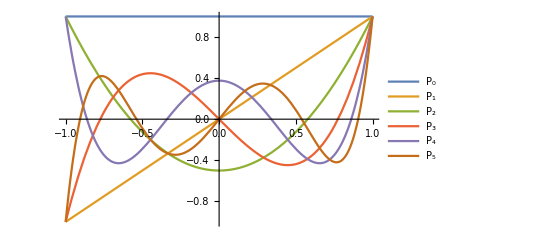

```mathematica
FewPolynomials = Table[LegendreP[i, x], {i, 0, 5}]
Plot[FewPolynomials, {x, -1, 1}, PlotLegends->{Table[Subscript[P, i], {i, 0, 5}]}]
```

{1,Cos[x],1/2 (-1+3 Cos[x]^2),1/2 (-3 Cos[x]+5 Cos[x]^3),1/8 (3-30 Cos[x]^2+35 Cos[x]^4),1/8 (15 Cos[x]-70 Cos[x]^3+63 Cos[x]^5)}

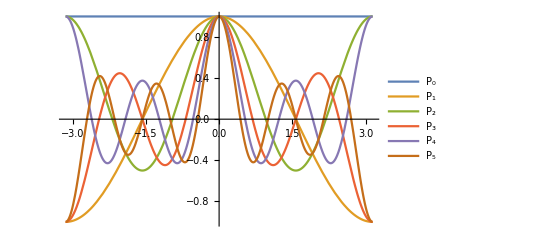

```mathematica
FewPolynomials = Table[LegendreP[i, Cos[x]], {i, 0, 5}]
Plot[FewPolynomials, {x, -Pi, Pi}, PlotLegends->{Table[Subscript[P, i], {i, 0, 5}]}]
```

## Associate Legendre Polynomials P_n^k(x)

{{1,0,0,0,0},{x,-√(1-x^2),0,0,0},{1/2 (-1+3 x^2),-3 x √(1-x^2),-3 (-1+x^2),0,0},{1/2 (-3 x+5 x^3),-3/2 √(1-x^2) (-1+5 x^2),-15 x (-1+x^2),-15 (1-x^2)^(3/2),0},{1/8 (3-30 x^2+35 x^4),-5/2 √(1-x^2) (-3 x+7 x^3),-15/2 (-1+x^2) (-1+7 x^2),-105 x (1-x^2)^(3/2),105 (-1+x^2)^2}}

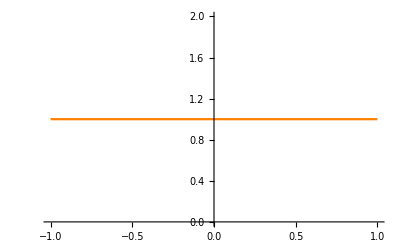
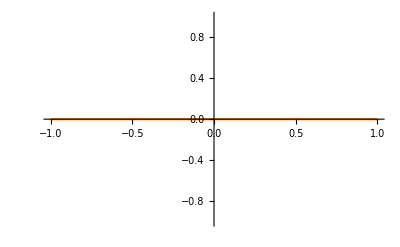
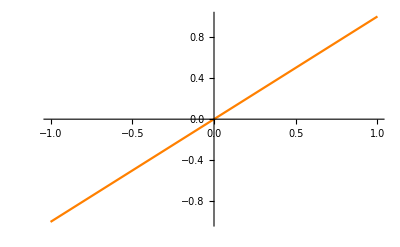
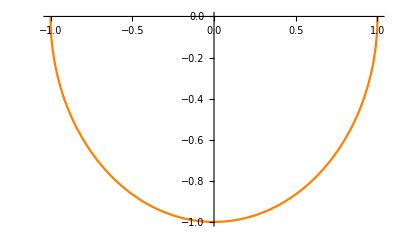
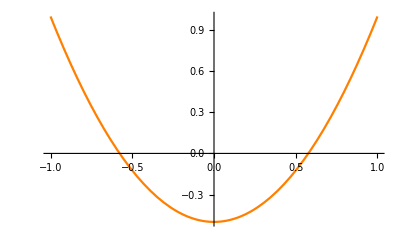
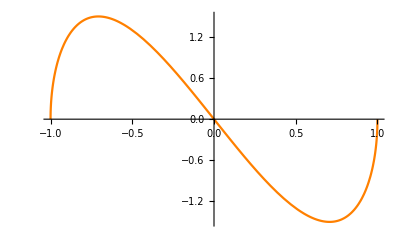
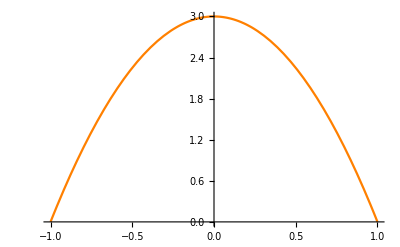
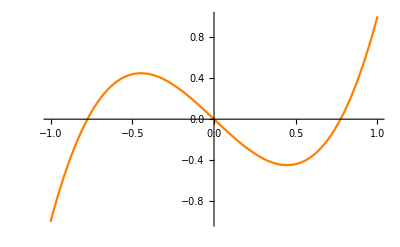
{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
FewAssoPolynomials = Table[LegendreP[n,k, x], {n, 0, 4},{k, 0, 4} ]
Table[Plot[LegendreP[n, k, x],{x, -1, 1}, PlotStyle->Orange],{n, 0, 4}, {k, 0, 4}]
```

## Orthogonality of P_n(x) and P_n^k(x)

```mathematica
Integrate[LegendreP[0, x]*LegendreP[1, x], {x, -1, 1}]
```

0

```mathematica
Integrate[LegendreP[1, x]*LegendreP[1, x], {x, -1, 1}]
```

2/3

```mathematica
Integrate[LegendreP[1, 1, x]*LegendreP[2, 1, x], {x, -1, 1}]
```

0

```mathematica
Integrate[LegendreP[1, 1, x]*LegendreP[1, 1, x], {x, -1, 1}]
```

```mathematica
4/3
```

```mathematica
Integrate[(LegendreP[2,1 , x]*LegendreP[2,1, x]), {x, -1, 1}]
```

12/5

```mathematica
Integrate[(LegendreP[3,2 , x]*LegendreP[3,2, x])/(1+(x^2)), {x, -1, 1}]
```

-90 (-16+5 π)

```mathematica
Integrate[(LegendreP[3,0 , x]*LegendreP[3,0, x])/(1+(x^2)), {x, -1, 1}]
```

76/3-8 π

## Fourier-Legendre Series

Objectives:

To obtain Fourier constants in Fourier-Legendre Series of the function Sin(2πx)

To obtain m^th partial sum of the FL series of the above function and plot it 4 values of m

$Aborted

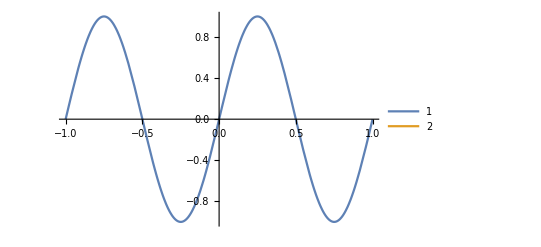

```mathematica
f[x_] :=Sin[2Pi*x]
a[m_]:= (2m+1)/2 *Integrate[f[x]*LegendreP[m, x], {x, -1, 1}]
FLMthPartialSum[M_] = ∑_(m=0)^M a[m]*LegendreP[m, x] //Simplify
Plot[{f[x], Table[FLMthPartialSum[M], {M, 0, 5}]}, {x, -1, 1}, PlotLegends->Automatic]
```